## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/SinJe LPT 2016/img/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->12,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
BostonBlue=RGBColor["#00688B"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->True,FrameStyle->st,AxesStyle->st,PlotRange->All];
```

## Diffraction of 1D cut & project sets

```mathematica
α=N[1/GoldenRatio];
θ=N[ArcTan[α]];
```

```mathematica
a=Cos[θ];
b=Sin[θ];
(* width of the window *)
W=a+b;
(* go from {n,m} to {p_(//),p_⊥} *)
ppara[n_,m_]:=a n + b m
pperp[n_,m_]:=-b n + a m
```

```mathematica
(* the intensity of the Bragg peak created by the point {n,m} of the dual lattice *)
int[n_,m_]:=W^2Sinc[π W pperp[n,m]]^2
```

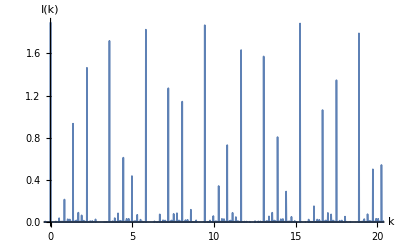

```mathematica
L=40;
(* intensities created by the dual lattice points in the square of size 2L centred about the origin *)
intensities=Flatten[Table[{ppara[n,m],int[n,m]},{n,-L,L},{m,-L,L}],1];
intensities=Sort[intensities];
ListPlot[intensities,Joined->True,PlotRange->{{0,20},All},Frame->False,AxesLabel->{"k","I(k)"},PlotStyle->Thickness[0.003]]
```

```mathematica
Export[NotebookDirectory[]<>"diffraction_fibonacci.pdf",%]
```

/home/nicolas/git/talks/SinJe LPT 2016/img/diffraction_fibonacci.pdf